```mathematica
dat={{1,0,1,17.71},{1,2,1,-18.94},{0,1,1,-23.5},{1,2,2,28},{1,2,3,5.11},{1,4,3,-3.05},{0,3,3,-2.27},{1,4,4,4.94},{1,4,5,0.36},{1,1,0,-1.83},{0,0,0,4.53},{1,1,1,-22.69},{1,1,2,16.18},{1,3,2,1.03},{0,2,2,7.34},{1,3,3,-2.66},{1,3,4,1.69},{1,5,4,0.33},{0,4,4,1.06},{1,5,5,-0.86},{1,5,6,0.19}};
```

```mathematica
pw=Table[0,{J,0,6},{L,0,5},{S,0,1}];
```

```mathematica
For[i=1,i<22,i++,pw[[dat[[i,3]]+1,dat[[i,2]]+1,dat[[i,1]]+1]]=dat[[i,4]]]
```

```mathematica
pw
```

{{{4.53,0},{0,-1.83},{0,0},{0,0},{0,0},{0,0}},{{0,17.71},{-23.5,-22.69},{0,-18.94},{0,0},{0,0},{0,0}},{{0,0},{0,16.18},{7.34,28},{0,1.03},{0,0},{0,0}},{{0,0},{0,0},{0,5.11},{-2.27,-2.66},{0,-3.05},{0,0}},{{0,0},{0,0},{0,0},{0,1.69},{1.06,4.94},{0,0.33}},{{0,0},{0,0},{0,0},{0,0},{0,0.36},{0,-0.86}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0.19}}}

```mathematica
Grid[pw]
```

{4.53,0} | {0,-1.83} | {0,0} | {0,0} | {0,0} | {0,0}
{0,17.71} | {-23.5,-22.69} | {0,-18.94} | {0,0} | {0,0} | {0,0}
{0,0} | {0,16.18} | {7.34,28} | {0,1.03} | {0,0} | {0,0}
{0,0} | {0,0} | {0,5.11} | {-2.27,-2.66} | {0,-3.05} | {0,0}
{0,0} | {0,0} | {0,0} | {0,1.69} | {1.06,4.94} | {0,0.33}
{0,0} | {0,0} | {0,0} | {0,0} | {0,0.36} | {0,-0.86}
{0,0} | {0,0} | {0,0} | {0,0} | {0,0} | {0,0.19}

```mathematica
sing=Table[0,{i,0,5}];
trip=Table[0,{i,0,5}];
```

```mathematica
For[i=1,i<7,i++,sing[[i]]=pw[[i,i,1]]]
trip[[1]]=pw[[2,1,2]];
For[i=2,i<7,i++,trip[[i]]=(pw[[i,i,2]]+pw[[i+1,i,2]]+pw[[i-1,i,2]])/3]
```

```mathematica
sing
```

{4.53,-23.5,7.34,-2.27,1.06,0}

```mathematica
trip
```

{17.71,-2.78,4.72333,0.02,0.75,-0.113333}

```mathematica
f[θ_,pshifts_]:=1/(2 I κ/ℏc) Sum[(2 L +1) LegendreP[L,Cos[θ]] (Exp[2 I pshifts[[L+1]]]-1),{L,0,5}]
```

```mathematica
f[0,sing]+f[Pi,trip]
```

8.53302+17.7124 ⅈ

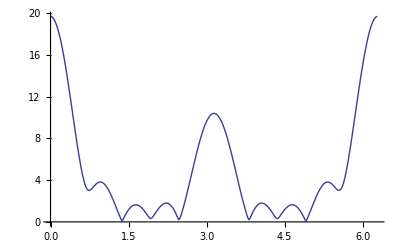

```mathematica
Plot[Abs[f[θ,sing]+f[Pi-θ,trip]],{θ,0,2 Pi}]
```